# Chapter 2: Vector and Matrices in Mathematica

## Since now we are familiar with the essentials of Mathematica, let’s apply that knowledge to some of the physical problems

## Electric Fields

I am assuming the reader is familiar with the undergraduate physics and that’s why I won’t be defining each and every term here.  

In this section, we are going to find and visualise electric field at a point P because of a charge q

```mathematica
r={x,y,z} (*We are going to define r vector in this way*)
```

{x,y,z}

If you don’t want see output after every input just add “;” after every input

```mathematica
r1 = {x1,y1,z1};
```

```mathematica
r-r1
```

{x-x1,y-y1,z-z1}

```mathematica
r r1 (*This will give the dot product*)
```

{x x1,y y1,z z1}

```mathematica
(r-r1)(r-r1)(*This is the square of the distance between the points*)
```

{(x-x1)^2,(y-y1)^2,(z-z1)^2}

```mathematica
Cross[r,r1]
```

{-y1 z+y z1,x1 z-x z1,-x1 y+x y1}

Alright, let’s define the electric field

```mathematica
Efield1[q1_,r1_,r_]:= (q1/((r-r1).(r-r1))^(3/2)) (r-r1)
```

```mathematica
Efield1[q1,r1,r]
```

{(q1 (x-x1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))}

```mathematica
Efield[1,{1,1,0},{x,y,0}]
```

{(-1+x)/(((-1+x)^2+(-1+y)^2)^(3/2)),(-1+y)/(((-1+x)^2+(-1+y)^2)^(3/2)),0}

Now we are going to use VectorPlot for plotting the electric field and for that we need Ex and Ey separately and for that we are going to use the Take function

```mathematica
?Take
```

```mathematica
{Ex,Ey}=Take[Efield1[1,{1,1,0},{x,y,0}],2]
```

{(-1+x)/(((-1+x)^2+(-1+y)^2)^(3/2)),(-1+y)/(((-1+x)^2+(-1+y)^2)^(3/2))}

```mathematica
Ex
```

(-1+x)/(((-1+x)^2+(-1+y)^2)^(3/2))

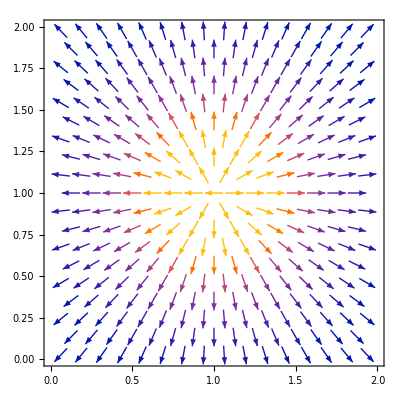

```mathematica
VectorPlot[{Ex,Ey},{x,0,2},{y,0,2},Axes->True]
```

Let’s take a bit more complicated field

```mathematica
Efield2[q2_,r2_,r_]:= (q2/((r-r2).(r-r2))^(3/2)) (r-r2)
```

```mathematica
Efield2[q2,r2,r]
```

{(q2 (-r2+x))/(((-r2+x)^2+(-r2+y)^2+(-r2+z)^2)^(3/2)),(q2 (-r2+y))/(((-r2+x)^2+(-r2+y)^2+(-r2+z)^2)^(3/2)),(q2 (-r2+z))/(((-r2+x)^2+(-r2+y)^2+(-r2+z)^2)^(3/2))}

```mathematica
Etotal[q1_,q2_,r1_,r2_,r_]:=Efield1[q1,r1,r]+Efield2[q2,r2,r]
```

If I take q1=-q2 then I will the dipole, and let’s have distance between them to be 1 unit

```mathematica
{Edipx,Edipy}=Take[Etotal[1,-1,{0.5,1,0},{1.5,1,0},{x,y,0}],2];
```

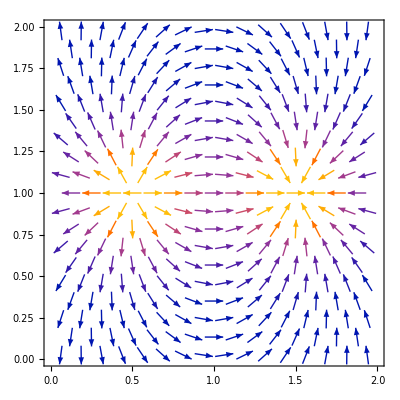

```mathematica
VectorPlot[{Edipx,Edipy},{x,0,2},{y,0,2}]
```

Let’s have 3D plot of these electric fields

```mathematica
{Ex3D,Ey3D, Ez3D} = Efield[{x,y,z},{0,0,0},1]
```

{x/(3 √3),y/(3 √3),z/(3 √3)}

```mathematica
VectorPlot3D[{Ex3D,Ey3D, Ez3D},{x,-2,2},{y,-2,2},{z,-2,2},VectorScale->{Small,0.4}] (*Change the size of arrows using the VectorScale function*)
```

-Graphics3D-

```mathematica
{Ex3D,Ey3D, Ez3D} = Etotal[1,-1,{0.5,1,0},{1.5,1,0},{x,y,0}]
```

{-(-1.5+x)/(((-1.5+x)^2+(-1+y)^2)^(3/2))+(-0.5+x)/(((-0.5+x)^2+(-1+y)^2)^(3/2)),-(-1+y)/(((-1.5+x)^2+(-1+y)^2)^(3/2))+(-1+y)/(((-0.5+x)^2+(-1+y)^2)^(3/2)),0}

```mathematica
VectorPlot3D[{Ex3D,Ey3D, Ez3D},{x,-2,2},{y,-2,2},{z,-2,2},VectorScale->{Small,0.1}] (*Change the size of arrows using the VectorScale function*)
```

-Graphics3D-

## Matrices

```mathematica
m = {{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}}(*This is a matrix*)
```

{{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}}

To see this in a matrix form we will use MatrixForm function

```mathematica
MatrixForm[m]
```

(a11 | a12 | a13
a21 | a22 | a23
a31 | a32 | a33)

```mathematica
a={{1,2,3},{-1,4,5},{6,-1,5}};
b={{9,-2,1},{-5,5,0},{-1,-2,1}};
```

```mathematica
a b //MatrixForm
```

(9 | -4 | 3
5 | 20 | 0
-6 | 2 | 5)

```mathematica
Det[a]
```

26

```mathematica
Ainv = Inverse[a]
```

{{25/26,-1/2,-1/13},{35/26,-1/2,-4/13},{-23/26,1/2,3/13}}

```mathematica
Ainv.a//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Transpose[a]
```

{{1,-1,6},{2,4,-1},{3,5,5}}

```mathematica
Part[a,2,1](*This gives Subscript[a, ij] based on the input i and j*)
```

-1

## Normal Modes

•	Setting up the equations of motion, often using Newton’s laws or the Lagrangian formalism.
	•	Linearizing those equations around an equilibrium configuration.
	•	Expressing them in matrix form, typically involving a mass matrix M and a stiffness matrix K.
	•	Solving the eigenvalue problem (K - ω^2 M) X = 0 to find the normal mode frequencies ω and the corresponding eigenvectors (mode shapes).
	
	
	Let’s start the discussion with two mass blocks

```mathematica
mat= {{k-m w^2,-k},{-k,k-m w^2}}
```

{{k-m w^2,-k},{-k,k-m w^2}}

```mathematica
sol = Solve[Det[mat]==0,w]
```

{{w→0},{w→0},{w→-(√2 √k)/(√m)},{w→(√2 √k)/(√m)}}

Analysis is easy for two mass but what if we introduce five masses

```mathematica
m5={{k-m w^2,-k,0,0,0},{-k,2 k-m w^2,-k,0,0},{0,-k,2 k-m w^2,-k,0},{0,0,-k,2 k-m w^2,-k},{0,0,0,-k,k-m w^2}};
```

```mathematica
sol = Solve[Det[m5]==0,w]
```

{{w→0},{w→0},{w→-(√((3 k)/m-(√5 k)/m))/(√2)},{w→(√((3 k)/m-(√5 k)/m))/(√2)},{w→-(√((5 k)/m-(√5 k)/m))/(√2)},{w→(√((5 k)/m-(√5 k)/m))/(√2)},{w→-(√((3 k)/m+(√5 k)/m))/(√2)},{w→(√((3 k)/m+(√5 k)/m))/(√2)},{w→-(√((5 k)/m+(√5 k)/m))/(√2)},{w→(√((5 k)/m+(√5 k)/m))/(√2)}}

## Logical Operators

If [test, e1, e2] : gives e1 if test succeeds and e2 if it fails
| | : logical operator ‘or’
&& : logical operator ‘and’
! : logical operator ‘not’

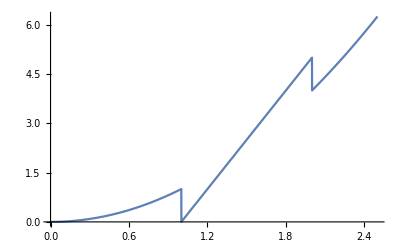

```mathematica
g[t_]:=If[t>1&&t<2,5(t-1),t^2];
Plot[g[t],{t,0,2.5},PlotRange->All]
```

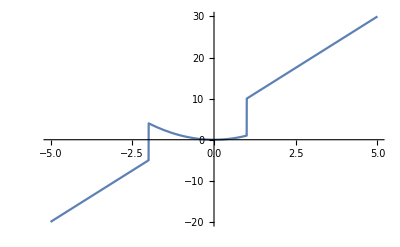

```mathematica
g[t_]:=If[t>1||t<-2,5(t+1),t^2];
Plot[g[t],{t,-5,5},PlotRange->All]
```